# Robot antropomorfo

## Cinematica diretta 3DOF

```mathematica
tab={{Subscript[q, 1],Subscript[L, 1],Pi/2,0},{Subscript[q, 2],0,0,Subscript[L, 2]},{Subscript[q, 3],0,0,Subscript[L, 3]}};
TableForm[tab,TableHeadings->{{"1","2","3"},{"θ","d","α","a"}}]
```

| θ | d | α | a
1 | q_1 | L_1 | π/2 | 0
2 | q_2 | 0 | 0 | L_2
3 | q_3 | 0 | 0 | L_3

```mathematica
Q03=cinematicaDiretta[tab];
h03=Q03[[1;;3,4]];
Q03/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i],Cos[Subscript[q, i_]+Subscript[q, j_]]->Subscript[c, i,j],Sin[Subscript[q, i_]+Subscript[q, j_]]->Subscript[s, i,j]}//MatrixForm
```

(c_1 c_(2,3) | -c_1 s_(2,3) | s_1 | c_1 (c_2 L_2+L_3 c_(2,3))
s_1 c_(2,3) | -s_1 s_(2,3) | -c_1 | s_1 (c_2 L_2+L_3 c_(2,3))
s_(2,3) | c_(2,3) | 0 | L_1+L_2 s_2+L_3 s_(2,3)
0 | 0 | 0 | 1)

## Cinematica diretta 6DOF

```mathematica
tab2={{Subscript[q, 1],Subscript[L, 1],Pi/2,0},{Subscript[q, 2],0,0,Subscript[L, 2]},{Subscript[q, 3],0,Pi/2,Subscript[L, 3]},{Subscript[q, 4],Subscript[L, 4],Pi/2,0},{Subscript[q, 5],0,-Pi/2,0},{Subscript[q, 6],Subscript[L, 6],0,0}};
tab2//MatrixForm
```

(q_1 | L_1 | π/2 | 0
q_2 | 0 | 0 | L_2
q_3 | 0 | π/2 | L_3
q_4 | L_4 | π/2 | 0
q_5 | 0 | -π/2 | 0
q_6 | L_6 | 0 | 0)

```mathematica
cinematicaDiretta[tab2]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i],Cos[Subscript[q, i_]+Subscript[q, j_]]->Subscript[c, i,j],Sin[Subscript[q, i_]+Subscript[q, j_]]->Subscript[s, i,j]}//MatrixForm
```

(s_1 (c_5 c_6 s_4+c_4 s_6)+c_1 ((c_4 c_5 c_6-s_4 s_6) c_(2,3)+c_6 s_5 s_(2,3)) | c_6 (c_4 s_1-c_1 s_4 c_(2,3))-s_6 (c_5 s_1 s_4+c_1 (c_4 c_5 c_(2,3)+s_5 s_(2,3))) | -s_5 (s_1 s_4+c_1 c_4 c_(2,3))+c_1 c_5 s_(2,3) | L_6 (-s_5 (s_1 s_4+c_1 c_4 c_(2,3))+c_1 c_5 s_(2,3))+c_1 (c_2 L_2+L_3 c_(2,3)+L_4 s_(2,3))
-c_1 (c_5 c_6 s_4+c_4 s_6)+s_1 (c_4 c_5 c_6-s_4 s_6) c_(2,3)+c_6 s_1 s_5 s_(2,3) | c_1 (-c_4 c_6+c_5 s_4 s_6)-s_1 ((c_6 s_4+c_4 c_5 s_6) c_(2,3)+s_5 s_6 s_(2,3)) | s_5 (c_1 s_4-c_4 s_1 c_(2,3))+c_5 s_1 s_(2,3) | s_1 (c_2 L_2+L_3 c_(2,3)+L_4 s_(2,3))+L_6 (s_5 (c_1 s_4-c_4 s_1 c_(2,3))+c_5 s_1 s_(2,3))
-s_4 s_6 s_(2,3)+c_6 (-s_5 c_(2,3)+c_4 c_5 s_(2,3)) | -c_6 s_4 s_(2,3)+s_6 (s_5 c_(2,3)-c_4 c_5 s_(2,3)) | -c_5 c_(2,3)-c_4 s_5 s_(2,3) | L_1+L_2 s_2-(L_4+c_5 L_6) c_(2,3)+(L_3-c_4 L_6 s_5) s_(2,3)
0 | 0 | 0 | 1)

## Cinematica inversa

```mathematica
(*Siano x,y,z le coordinate dell'end-effector desiderate*)
{e1,e2,e3}=TrigExpand[{x,y,z}-h03]/.{Cos[Subscript[q, i_]]->Subscript[c, i],Sin[Subscript[q, i_]]->Subscript[s, i]};
e4=Subscript[c, 1]^2+Subscript[s, 1]^2-1;
e5=Subscript[c, 2]^2+Subscript[s, 2]^2-1;
e6=Subscript[c, 3]^2+Subscript[s, 3]^2-1;
TableForm[{e1,e2,e3}]
```

x-c_1 c_2 L_2-c_1 c_2 c_3 L_3+c_1 L_3 s_2 s_3
y-c_2 L_2 s_1-c_2 c_3 L_3 s_1+L_3 s_1 s_2 s_3
z-L_1-L_2 s_2-c_3 L_3 s_2-c_2 L_3 s_3

### Calcolo q_3

```mathematica
sol=GroebnerBasis[{e1,e2,e3,e4,e5,e6},{Subscript[c, 3],Subscript[s, 3]},{Subscript[c, 1],Subscript[s, 1],Subscript[c, 2],Subscript[s, 2],Subscript[s, 3]},CoefficientDomain->RationalFunctions];
Solve[sol==0,Subscript[c, 3]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3}//FullSimplify
Solve[e6==0,Subscript[s, 3]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3,Subscript[c, 3]->c3}
```

{{c_3→(-l2^2-l3^2+x^2+y^2+(l1-z)^2)/(2 l2 l3)}}

{{s_3→-√(1-c3^2)},{s_3→√(1-c3^2)}}

```mathematica
(*Siccome -1≤Subscript[c, 3]≤1, -1≤(l1^2-l2^2-l3^2+x^2+y^2-2 l1 z+z^2)/(2 l2 l3)≤1*)
```

#### L_2 L_3==0

```mathematica
TableForm[{x-Q03[[1,4]],y-Q03[[2,4]],z-Q03[[3,4]]}]/.{Subscript[L, 2]->0}
TableForm[{x-Q03[[1,4]],y-Q03[[2,4]],z-Q03[[3,4]]}]/.{Subscript[L, 3]->0}
```

x-Cos[q_1] Cos[q_2+q_3] L_3
y-Cos[q_2+q_3] Sin[q_1] L_3
z-L_1-Sin[q_2+q_3] L_3

x-Cos[q_1] Cos[q_2] L_2
y-Cos[q_2] Sin[q_1] L_2
z-L_1-Sin[q_2] L_2

```mathematica
(*Segue che se (Subscript[L, 2]==0 || Subscript[L, 3]==0) il robot perde un grado di libertà. Impongo dunque che Subscript[L, 2]≠0 e Subscript[L, 3]≠0*)
```

### Calcolo q_2

```mathematica
sol=GroebnerBasis[{e1,e2,e3,e5},{Subscript[c, 2],Subscript[s, 2]},{Subscript[c, 1],Subscript[s, 1]},CoefficientDomain->RationalFunctions]//TableForm
```

-z^2+2 z L_1-L_1^2+(2 z L_2-2 L_1 L_2+2 z c_3 L_3-2 c_3 L_1 L_3) s_2+L_3^2 s_3^2+s_2^2 (-L_2^2-2 c_3 L_2 L_3-c_3^2 L_3^2-L_3^2 s_3^2)
z-L_1+(-L_2-c_3 L_3) s_2-c_2 L_3 s_3

```mathematica
Solve[sol[[1,1]]==0,Subscript[s, 2]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3,Subscript[c, 3]->c3,Subscript[s, 3]->s3}//FullSimplify
Solve[sol[[1,2]]==0,Subscript[c, 2]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3,Subscript[s, 2]->s2,Subscript[c, 3]->c3,Subscript[s, 3]->s3}//FullSimplify
```

{{s_2→-(√(l3^2 s3^2 ((l2+c3 l3)^2+l3^2 s3^2-(l1-z)^2))+(l2+c3 l3) (l1-z))/((l2+c3 l3)^2+l3^2 s3^2)},{s_2→(√(l3^2 s3^2 ((l2+c3 l3)^2+l3^2 s3^2-(l1-z)^2))-(l2+c3 l3) (l1-z))/((l2+c3 l3)^2+l3^2 s3^2)}}

{{c_2→-(l1+l2 s2+c3 l3 s2-z)/(l3 s3)}}

```mathematica
sol=((l2+c3 l3)^2+l3^2 s3^2-(l1-z)^2)/.{s3->√(1-c3^2)};
sol/.{c3->1/(2 l2 l3)(l1^2-l2^2-l3^2+x^2+y^2-2 l1 z+z^2)}//FullSimplify
```

x^2+y^2

```mathematica
(*Segue dunque che l3^2 s3^2 ((l2+c3 l3)^2+l3^2 s3^2-(l1-z)^2)≥0 ∀q_(3,)Subscript[L, 2],Subscript[L, 3]∈R^3*)
```

#### (L_2+c_3 L_3)^2+L_3^2 s_3^2==0

```mathematica
(*Andiamo innanzitutto a determinare quando (Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2==0, supponendo che Subscript[L, 2]≠0 e Subscript[L, 3]≠0 per quanto detto in precedenza*)
Solve[{(Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2,e6}==0,{Subscript[c, 3],Subscript[s, 3]}]
```

{{c_3→(-L_2^2-L_3^2)/(2 L_2 L_3),s_3→-(ⅈ (L_2^2-L_3^2))/(2 L_2 L_3)},{c_3→(-L_2^2-L_3^2)/(2 L_2 L_3),s_3→(ⅈ (L_2^2-L_3^2))/(2 L_2 L_3)}}

```mathematica
Solve[{(Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2,e6}==0,{Subscript[c, 3],Subscript[s, 3]}]/.{Subscript[L, 3]->Subscript[L, 2]}
Solve[{(Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2,e6}==0,{Subscript[c, 3],Subscript[s, 3]}]/.{Subscript[L, 3]->-Subscript[L, 2]}
```

{{c_3→-1,s_3→0},{c_3→-1,s_3→0}}

{{c_3→1,s_3→0},{c_3→1,s_3→0}}

```mathematica
(*Calcoliamo le equazioni dell'antropomorfo quando (Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2==0*)
TableForm[{e1,e2,e3}]/.{Subscript[c, 3]->-1,Subscript[s, 3]->0,Subscript[L, 3]->Subscript[L, 2]}
TableForm[{e1,e2,e3}]/.{Subscript[c, 3]->-1,Subscript[s, 3]->0,Subscript[L, 3]->Subscript[L, 2]}
```

x
y
z-L_1

x
y
z-L_1

```mathematica
(*Segue dunque che se (Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2==0 Subscript[q, 2] è arbitrario*)
```

### Calcolo q_1

```mathematica
Solve[e1==0,Subscript[c, 1]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3,Subscript[c, 2]->c2,Subscript[s, 2]->s2,Subscript[c, 3]->c3,Subscript[s, 3]->s3}//FullSimplify
Solve[e2==0,Subscript[s, 1]]/.{Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3,Subscript[c, 2]->c2,Subscript[s, 2]->s2,Subscript[c, 3]->c3,Subscript[s, 3]->s3}//FullSimplify
```

{{c_1→x/(c2 l2+c2 c3 l3-l3 s2 s3)}}

{{s_1→y/(c2 l2+c2 c3 l3-l3 s2 s3)}}

#### c_2 L_2+c_2 c_3 L_3-L_3 s_2 s_3==0

```mathematica
Assuming[Subscript[c, 2] Subscript[L, 2]+Subscript[c, 2] Subscript[c, 3] Subscript[L, 3]-Subscript[L, 3] Subscript[s, 2] Subscript[s, 3]==0,TableForm[FullSimplify[{e1,e2,e3}]]]
```

x
y
z-L_1-(L_2+c_3 L_3) s_2-c_2 L_3 s_3

```mathematica
(*Segue dunque che se Subscript[c, 2] Subscript[L, 2]+Subscript[c, 2] Subscript[c, 3] Subscript[L, 3]-Subscript[L, 3] Subscript[s, 2] Subscript[s, 3]==0 Subscript[q, 1] è arbitrario*)
```

### Procedura

```mathematica
(*Questa procedura calcola le variabili di giunto corrispondenti alla posizione dell’end effector (x,y,z) fornita in ingresso.
I parametri l1,l2 e l3 rappresentano le lunghezze dei segmenti Subscript[L, 1],Subscript[L, 2] e Subscript[L, 3] del robot,mentre g2 e g3, pari a ±1, permettono di scegliere una tra le diverse configurazioni ammissibili*)
cinInversaAntro[x_,y_,z_,l1_,l2_,l3_,g2_,g3_]:=Module[{c1,s1,c2,s2,c3,s3,q1,q2,q3},
If[AllTrue[{x,y,z,l1,l2,l3},numeroReale] &&(g2===1 ||g2===-1)&&(g3===1 ||g3===-1),
If[N[FullSimplify[l2*l3]]=!=0.,
If[TrueQ[Refine[FullSimplify[(-l2^2-l3^2+x^2+y^2+(l1-z)^2)/(2 l2 l3)+1]>=0]] && TrueQ[Refine[FullSimplify[(-l2^2-l3^2+x^2+y^2+(l1-z)^2)/(2 l2 l3)-1]<=0]],

c3=(-l2^2-l3^2+x^2+y^2+(l1-z)^2)/(2 l2 l3);
s3=g3*√Abs[1-c3^2];
q3=ArcTan[c3,s3]//FullSimplify;


If[N[FullSimplify[(l2+c3 l3)^2+l3^2 s3^2]]=!=0.,
s2=(g2 √(l3^2 s3^2 ((l2+c3 l3)^2+l3^2 s3^2-(l1-z)^2))-(l2+c3 l3) (l1-z))/((l2+c3 l3)^2+l3^2 s3^2);

c2=-(l1+l2 s2+c3 l3 s2-z)/(l3 s3);
q2=ArcTan[c2,s2]//FullSimplify;,
q2=0;(*Se (l2+c3 l3)^2+l3^2 s3^2===0 q2 è arbitrario*)];

If[N[FullSimplify[c2 l2+c2 c3 l3-l3 s2 s3]]=!=0., 
c1=x/(c2 l2+c2 c3 l3-l3 s2 s3);
s1=y/(c2 l2+c2 c3 l3-l3 s2 s3);
q1=ArcTan[c1,s1]//FullSimplify;,
q1=0;(*Se c2 l2+c2 c3 l3-l3 s2 s3===0 q1 è arbitrario*)];
{q1,q2,q3},

Echo[{},"Il punto indicato è all'infuori dello spazio operativo"]],
Echo["l2 e l3 devono essere diversi da 0"];],
Echo["Argomenti non validi"];]]
```

## Test cinematica inversa

```mathematica
(*scelgo arbitrariamente le coordinate dell'end effector*)
Q1=1;
Q2=2;
Q3=1;
L1=1;
L2=1;
L3=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
Echo[{xx,yy,zz},"Coordinate"];
```

Coordinate  {-1.29464,-2.01628,2.19154}

```mathematica
Echo[cinInversaAntro[xx,yy,zz,L1,L2,L3,+1,+1],"gomito ++"];
Echo[cinInversaAntro[xx,yy,zz,L1,L2,L3,+1,-1],"gomito +-"];
Echo[cinInversaAntro[xx,yy,zz,L1,L2,L3,-1,+1],"gomito -+"];
Echo[cinInversaAntro[xx,yy,zz,L1,L2,L3,-1,-1],"gomito --"];
```

gomito ++  {1.,2.,1.}

gomito +-  {-2.14159,1.14159,-1.}

gomito -+  {-2.14159,-0.218662,1.}

gomito --  {1.,-2.92293,-1.}

```mathematica
(*Da notare che la configurazione gomito +- mi restituisce le variabili di giunto iniziali*)
```

## Rappresentazione grafica

```mathematica
(*Questa funzione disegna lo spazio operativo del robot antropomorfo, che corrisponde ad una corona circolare di raggi pari a |l2-l3| e |l2+l3| centrata in (0,0,l1). I parametri dimX,dimY e dimZ indicano le dimensioni del plot*)
soAntropomorfo[l1_,l2_,l3_,dimX_,dimY_,dimZ_]:=Module[{r1,r2,plot1,plot2},
If[AllTrue[{l1,l2,l3,dimX,dimY,dimZ},NumericQ[#]&&!parteComplessa[#]&]&&AllTrue[{dimX,dimY,dimZ}, Positive],
If[N[FullSimplify[l2 l3]]=!=0.,

r1=Abs[l2-l3];
r2=Abs[l2+l3];

plot1=ContourPlot3D[x^2+y^2+(l1-z)^2==r1^2,{x,-dimX,dimX},{y,-dimY,dimY},{z,l1-dimZ,l1+dimZ},ContourStyle->Opacity[0.1,Blue],AxesLabel->{"x","y","z"}];
plot2=ContourPlot3D[x^2+y^2+(l1-z)^2==r2^2,{x,-dimX,dimX},{y,-dimY,dimY},{z,l1-dimZ,l1+dimZ},ContourStyle->Opacity[0.1,Gray],AxesLabel->{"x","y","z"}];
Show[plot1,plot2],

Echo["l2 e l3 devono essere diversi da 0"];],
Echo["Argomenti non validi"];]]
```

```mathematica
cinematicaDiretta[{tab[[1]]}]/.{Subscript[L, 1]->l1}//MatrixForm
cinematicaDiretta[tab[[1;;2]]]/. {Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[L, 1]->l1,Subscript[L, 2]->l2}//MatrixForm
cinematicaDiretta[tab[[1;;3]]]/. {Subscript[q, 1]->q1,Subscript[q, 2]->q2,Subscript[q, 3]->q3,Subscript[L, 1]->l1,Subscript[L, 2]->l2,Subscript[L, 3]->l3}//MatrixForm
```

(Cos[q_1] | 0 | Sin[q_1] | 0
Sin[q_1] | 0 | -Cos[q_1] | 0
0 | 1 | 0 | l1
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2] | -Cos[q1] Sin[q2] | Sin[q1] | l2 Cos[q1] Cos[q2]
Cos[q2] Sin[q1] | -Sin[q1] Sin[q2] | -Cos[q1] | l2 Cos[q2] Sin[q1]
Sin[q2] | Cos[q2] | 0 | l1+l2 Sin[q2]
0 | 0 | 0 | 1)

(Cos[q1] Cos[q2+q3] | -Cos[q1] Sin[q2+q3] | Sin[q1] | Cos[q1] (l2 Cos[q2]+l3 Cos[q2+q3])
Cos[q2+q3] Sin[q1] | -Sin[q1] Sin[q2+q3] | -Cos[q1] | (l2 Cos[q2]+l3 Cos[q2+q3]) Sin[q1]
Sin[q2+q3] | Cos[q2+q3] | 0 | l1+l2 Sin[q2]+l3 Sin[q2+q3]
0 | 0 | 0 | 1)

```mathematica
(*Questa procedura rappresenta il robot antropomorfo nello spazio. I parametri q1,q2 e q3 costituiscono le variabili di giunto del robot,l1,l2 e l3 rappresentano le lunghezze dei segmenti Subscript[L, 1],Subscript[L, 2] e Subscript[L, 3],mentre dimX,dimY e dimZ definiscono le dimensioni del plot.*)
robotAntropomorfo[q1_,q2_,q3_,l1_,l2_,l3_,dimX_,dimY_,dimZ_]:=Module[{x1,y1,z1,x2,y2,z2,x3,y3,z3,list,plot},
If[AllTrue[{q1,q2,q3,l1,l2,l3,dimX,dimY,dimZ}, NumericQ[#]&&!parteComplessa[#]&] && AllTrue[{dimX,dimY,dimZ},Positive],
If[N[FullSimplify[l2 l3]]=!=0.,

x1=0;
y1=0;
z1=l1;

x2=l2 Cos[q1] Cos[q2];
y2=l2 Cos[q2] Sin[q1];
z2=l1+l2 Sin[q2];

x3=Cos[q1] (l2 Cos[q2]+l3 Cos[q2+q3]);
y3=(l2 Cos[q2]+l3 Cos[q2+q3]) Sin[q1];
z3=l1+l2 Sin[q2]+l3 Sin[q2+q3];

list={{0,0,0},{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}};
plot = ListLinePlot3D[list, PlotRange->{{-dimX,dimX},{-dimY,dimY},{l1-dimZ,l1+dimZ}},PlotStyle->{Red,Thick},AxesLabel->{"x","y","z"}],

Echo["l2 e l3 devono essere diversi da 0"];],
Echo["Argomenti non validi"]]]
```

## Raggiungimento di un punto arbitrario

```mathematica
(*Questa procedura rappresenta graficamente il robot con l’end effector posizionato nel punto (x,y,z). Prende in ingresso le lunghezze del robot l1,l2 e l3, i suoi gomiti g2 e g3 ed una stringa s che specifica il titolo del grafico restituito in uscita*)
disegnoAntropomorfo[x_,y_,z_,l1_,l2_,l3_,g2_,g3_,s_]:=Module[{res, rr,p1, p2, p3},
If[StringQ[s],
res= cinInversaAntro[x,y,z,l1,l2,l3,g2,g3]//N;
If[!MatchQ[res,{_,_,_}],Abort[]];(*Argomenti non validi*)
Echo[res, s];

rr=Abs[l2]+Abs[l3];
p1=robotAntropomorfo[res[[1]],res[[2]],res[[3]],l1,l2,l3,rr,rr,rr];
If[!MatchQ[p1,_Graphics3D],Abort[]];(*Argomenti non validi*)
p2=ListPointPlot3D[{{x,y,z}},PlotStyle->Green];
p3 = soAntropomorfo[l1,l2,l3,rr,rr,rr];
Show[p1,p2,p3,PlotLabel->s],

Echo["Argomenti non validi"];]
]
```

```mathematica
(*Questa procedura rappresenta il robot mentre raggiunge il punto desiderato (x,y,z) in tutte le configurazioni cinematiche possibili.I parametri l1,l2 e l3 indicano le lunghezze dei segmenti del robot.*)
raggPuntoAntropomorfo[x_,y_,z_,l1_,l2_,l3_]:=Module[{p1,p2,p3,p4},
Echo[{x,y,z}, "Coordinate"];
p1=disegnoAntropomorfo[x,y,z,l1,l2,l3,+1,+1,"gomito ++"];
If[!MatchQ[p1,_Graphics3D],Abort[]];(*Argomenti non validi*)
p2=disegnoAntropomorfo[x,y,z,l1,l2,l3,+1,-1,"gomito +-"];
p3=disegnoAntropomorfo[x,y,z,l1,l2,l3,-1,+1,"gomito -+"];
p4=disegnoAntropomorfo[x,y,z,l1,l2,l3,-1,-1,"gomito --"];

GraphicsGrid[{{p1,p2},{p3,p4}}]
]
```

```mathematica
Q1=1;
Q2=2;
Q3=1;
L1=1;
L2=1;
L3=2;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
raggPuntoAntropomorfo[xx,yy,zz,L1,L2,L3]
```

Coordinate  {-1.29464,-2.01628,2.19154}

gomito ++  {1.,2.,1.}

gomito +-  {-2.14159,1.14159,-1.}

gomito -+  {-2.14159,-0.218662,1.}

gomito --  {1.,-2.92293,-1.}

-Graphics-

```mathematica
(*Si noti che, sebbene le configurazioni del robot antropomorfo sembrino a due a due uguali, in realtà l'orientamento dell'end-effector varia tra i quattro robot*)
```

```mathematica
(*Subscript[L, 2] e Subscript[L, 3] discordi*)
Q1=1;
Q2=2;
Q3=3;
L1=4;
L2=-2;
L3=3;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
raggPuntoAntropomorfo[xx,yy,zz,L1,L2,L3]
```

Coordinate  {0.90948,1.41643,-0.695368}

gomito ++  {-2.14159,1.31155,3.}

gomito +-  {1.,1.83004,-3.}

gomito -+  {1.,2.,3.}

gomito --  {-2.14159,1.14159,-3.}

-Graphics-

```mathematica
(*Singolarità Subscript[q, 1] e Subscript[q, 2] ((Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])^2+Subscript[L, 3]^2 Subscript[s, 3]^2==0 && Subscript[c, 2](Subscript[L, 2]+Subscript[c, 3] Subscript[L, 3])-Subscript[L, 3] Subscript[s, 2] Subscript[s, 3]==0)*)
L3=L2;
Q3=Pi;
xx=Q03[[1,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
yy=Q03[[2,4]]/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
zz=Q03[[3,4]]/.{Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
disegnoAntropomorfo[xx,yy,zz,L1,L2,L3,+1,+1,"Singolarità q_1 e q_2"]
```

Singolarità q_1 e q_2  {0.,0.,3.14159}

-Graphics3D-

```mathematica
(*Subscript[L, 2] Subscript[L, 3] == 0*)
L3=L2=1;
robotAntropomorfo[Q1,Q2,Q3,L1,0,L3,L3,L3,L3]
soAntropomorfo[L1,0,L3,L3,L3,L3]

robotAntropomorfo[Q1,Q2,Q3,L1,L2,0,L2,L2,L2]
soAntropomorfo[L1,L2,0,L3,L3,L3]
```

l2 e l3 devono essere diversi da 0

l2 e l3 devono essere diversi da 0

l2 e l3 devono essere diversi da 0

«1 more identical outputs»

## Animazione

```mathematica
(*Questa procedura realizza l’animazione di un robot antropomorfo che segue una traiettoria nello spazio descritta dalle funzioni px,py e pz. I parametri l1,l2 e l3 rappresentano le lunghezze del robot. 
N.B: Tale procedura non controlla gli argomenti passati in ingresso*)
animazioneAntropomorfo[px_,py_,pz_,l1_,l2_,l3_]:=Module[{q1,q2,q3,p1,p2,p3,rr},
rr=Abs[l2]+Abs[l3];
p3=soAntropomorfo[l1,l2,l3,rr,rr,rr];
Animate[
{q1,q2,q3}=cinInversaAntro[px[t],py[t],pz[t],l1,l2,l3,+1,+1];
p1=robotAntropomorfo[q1,q2,q3,l1,l2,l3,rr,rr,rr];
p2=ListPointPlot3D[{{px[t],py[t],pz[t]}},PlotStyle->Green];

Show[p1,p2,p3], {t, 0, 10, 0.01}, AnimationRate->0.2
]]
```

```mathematica
px[t_]:=2*Sin[t];
py[t_]:=2*Sin[t]*Cos[t];
pz[t_]:=Cos[t];
L1=-1;
L2=4;
L3=5;
animazioneAntropomorfo[px,py,pz,L1,L2, L3]
```

## Newton e gradiente

### Definizione della traiettoria reale e della traiettoria ideale

```mathematica
(*Definizione delle variabili*)
ω = 10;
Q1=1;
Q2=1/2;
Q3=2;
L1=1;
L2=2;
L3=3;
```

```mathematica
(*Definizione della traiettoria ideale che il robot vuole inseguire*)
xx3 =(h03[[1]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
yy3 =(h03[[2]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
zz3 =(h03[[3]]+Sin[ω*t]/2)/.{Subscript[q, 1]->Q1,Subscript[q, 2]->Q2,Subscript[q, 3]->Q3,Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3}//N;
TableForm[{xx3,yy3,zz3}]
```

-0.350259+0.5 Sin[10. t]
-0.545497+0.5 Sin[10. t]
3.75427+0.5 Sin[10. t]

```mathematica
(*Definizione della traiettoria reale che il robot può inseguire*)
{x3,y3,z3}=h03/.{Subscript[L, 1]->L1,Subscript[L, 2]->L2,Subscript[L, 3]->L3};
```

```mathematica
(*Stime iniziali*)
Subscript[q, 1,i]=Subscript[q, 1]+0.1 /.{Subscript[q, 1]->Q1}
Subscript[q, 2,i]=Subscript[q, 2]+0.1/.{Subscript[q, 2]->Q2}
Subscript[q, 3,i]=Subscript[q, 3]+0.1/.{Subscript[q, 3]->Q3}
```

1.1

0.6

2.1

```mathematica
tf=5;
λ=30;
μ=1/1000;
```

### Metodo di Newton

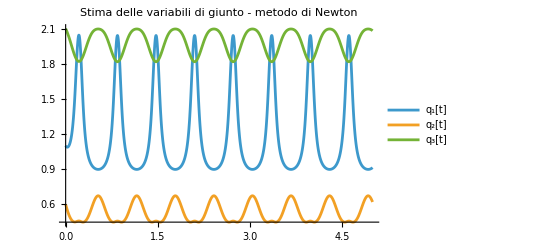

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "1",λ,μ, "Stima delle variabili di giunto - metodo di Newton","Traiettoria ideale e reale end effector - metodo di Newton"];
res[[1]]
res[[2]]
```

### Metodo del gradiente

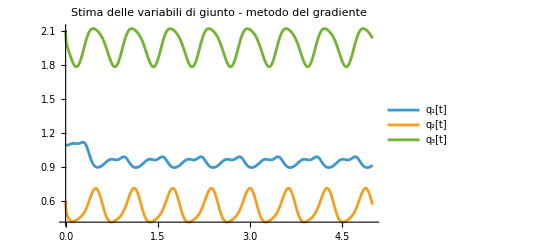

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "2",λ,μ, "Stima delle variabili di giunto - metodo del gradiente","Traiettoria ideale e reale end effector - metodo del gradiente"];
res[[1]]
res[[2]]
```

### Metodo misto

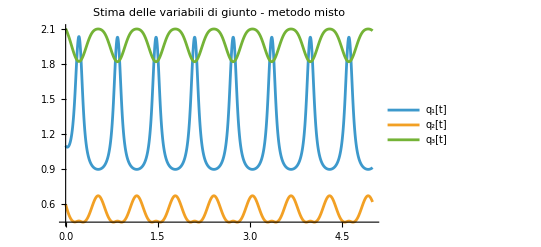

-Graphics-

```mathematica
res=osservatore[{xx3,yy3,zz3},{x3,y3,z3},t,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]},{Subscript[q, 1,i],Subscript[q, 2,i],Subscript[q, 3,i]},tf, "3",λ,μ, "Stima delle variabili di giunto - metodo misto","Traiettoria ideale e reale end effector - metodo misto"];
res[[1]]
res[[2]]
```

## Energia cinetica

```mathematica
xyz={{0,-Subscript[L, 1]/2,0},{-Subscript[L, 2]/2,0,0},{-Subscript[L, 3]/2,0,0}};
tab2=Join[tab,xyz,2];
TableForm[tab2,TableHeadings->{{"1","2","3"},{"θ","d","α","a","x","y","z"}}]
```

| θ | d | α | a | x | y | z
1 | q_1 | L_1 | π/2 | 0 | 0 | -L_1/2 | 0
2 | q_2 | 0 | 0 | L_2 | -L_2/2 | 0 | 0
3 | q_3 | 0 | 0 | L_3 | -L_3/2 | 0 | 0

```mathematica
{T,U}=energiaRobot[tab2,{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}];
```

Link1

B_ω  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B_t  (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

B  (I_(1y) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

T_1  1/2 I_(1y) (q_1')^2

T_2  0

T  1/2 I_(1y) (q_1')^2

U  4.905 m_1 L_1

Link2

B_ω  (c_2^2 I_(2y)+I_(2x) s_2^2 | 0 | 0
0 | I_(2z) | 0
0 | 0 | 0)

B_t  (1/4 c_2^2 m_2 L_2^2 | 0 | 0
0 | 1/4 m_2 L_2^2 | 0
0 | 0 | 0)

B  (I_(2x) s_2^2+1/4 c_2^2 (4 I_(2y)+m_2 L_2^2) | 0 | 0
0 | I_(2z)+1/4 m_2 L_2^2 | 0
0 | 0 | 0)

T_1  1/2 ((c_2^2 I_(2y)+I_(2x) s_2^2) (q_1')^2+I_(2z) (q_2')^2)

T_2  1/8 m_2 L_2^2 (c_2^2 (q_1')^2+(q_2')^2)

T  1/8 ((4 I_(2x) s_2^2+c_2^2 (4 I_(2y)+m_2 L_2^2)) (q_1')^2+(4 I_(2z)+m_2 L_2^2) (q_2')^2)

U  9.81 m_2 (L_1+(s_2 L_2)/2)

Link3

B_ω  (I_(3y) c_(2,3)^2+I_(3x) s_(2,3)^2 | 0 | 0
0 | I_(3z) | I_(3z)
0 | I_(3z) | I_(3z))

B_t  (1/4 m_3 (2 c_2 L_2+L_3 c_(2,3))^2 | 0 | 0
0 | 1/4 m_3 (4 L_2^2+4 c_3 L_2 L_3+L_3^2) | 1/4 m_3 L_3 (2 c_3 L_2+L_3)
0 | 1/4 m_3 L_3 (2 c_3 L_2+L_3) | 1/4 m_3 L_3^2)

B  (I_(3y) c_(2,3)^2+1/4 m_3 (2 c_2 L_2+L_3 c_(2,3))^2+I_(3x) s_(2,3)^2 | 0 | 0
0 | I_(3z)+1/4 m_3 (4 L_2^2+4 c_3 L_2 L_3+L_3^2) | I_(3z)+1/4 m_3 L_3 (2 c_3 L_2+L_3)
0 | I_(3z)+1/4 m_3 L_3 (2 c_3 L_2+L_3) | I_(3z)+1/4 m_3 L_3^2)

T_1  1/2 ((I_(3y) c_(2,3)^2+I_(3x) s_(2,3)^2) (q_1')^2+I_(3z) (q_2'+q_3')^2)

T_2  1/8 m_3 (4 L_2^2 (c_2^2 (q_1')^2+(q_2')^2)+4 L_2 L_3 (c_2 c_(2,3) (q_1')^2+c_3 q_2' (q_2'+q_3'))+L_3^2 (c_(2,3)^2 (q_1')^2+(q_2'+q_3')^2))

T  1/8 (4 ((I_(3y) c_(2,3)^2+I_(3x) s_(2,3)^2) (q_1')^2+I_(3z) (q_2'+q_3')^2)+m_3 (4 L_2^2 (c_2^2 (q_1')^2+(q_2')^2)+4 L_2 L_3 (c_2 c_(2,3) (q_1')^2+c_3 q_2' (q_2'+q_3'))+L_3^2 (c_(2,3)^2 (q_1')^2+(q_2'+q_3')^2)))

U  9.81 m_3 (L_1+s_2 L_2+1/2 Sin[q_2+q_3] L_3)

Risultati

Energia cinetica totale  1/8 ((4 I_(1y)+4 I_(2x) s_2^2+c_2^2 (4 I_(2y)+m_2 L_2^2)) (q_1')^2+(4 I_(2z)+m_2 L_2^2) (q_2')^2+4 ((Sin[q_2+q_3]^2 I_(3x)+Cos[q_2+q_3]^2 I_(3y)) (q_1')^2+I_(3z) (q_2'+q_3')^2)+m_3 (4 L_2^2 (c_2^2 (q_1')^2+(q_2')^2)+4 L_2 L_3 (Cos[q_2+q_3] c_2 (q_1')^2+c_3 q_2' (q_2'+q_3'))+L_3^2 (Cos[q_2+q_3]^2 (q_1')^2+(q_2'+q_3')^2)))

Energia potenziale gravitazionale totale  4.905 m_1 L_1+m_2 (9.81 L_1+4.905 s_2 L_2)+9.81 m_3 (L_1+s_2 L_2+1/2 Sin[q_2+q_3] L_3)

## Eulero Lagrange

```mathematica
F=1/2*{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'}.DiagonalMatrix[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3]}].{Subscript[q, 1]',Subscript[q, 2]',Subscript[q, 3]'};
euleroLagrange[T,U,F,{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[q, 1],Subscript[q, 2],Subscript[q, 3]}]//TableForm
```

f_1 q_1'+1/4 (Sin[2 q_2] (4 I_(2x)-4 I_(2y)-m_2 L_2^2) q_1' q_2'+4 Sin[2 (q_2+q_3)] (I_(3x)-I_(3y)) q_1' (q_2'+q_3')+4 (Sin[q_2+q_3]^2 I_(3x)+Cos[q_2+q_3]^2 I_(3y)) q_1''+(4 I_(1y)+4 Sin[q_2]^2 I_(2x)+Cos[q_2]^2 (4 I_(2y)+m_2 L_2^2)) q_1''+m_3 (2 Cos[q_2] L_2+Cos[q_2+q_3] L_3) (L_2 (-4 Sin[q_2] q_1' q_2'+2 Cos[q_2] q_1'')+L_3 (-2 Sin[q_2+q_3] q_1' (q_2'+q_3')+Cos[q_2+q_3] q_1'')))==u_1
1/8 (4 (Sin[2 q_2] (-I_(2x)+I_(2y))+Sin[2 (q_2+q_3)] (-I_(3x)+I_(3y))) (q_1')^2+m_2 L_2 (39.24 Cos[q_2]+L_2 (1. Sin[2 q_2] (q_1')^2+2 q_2''))+8 (f_2 q_2'+(I_(2z)+I_(3z)) q_2''+I_(3z) q_3'')+m_3 (L_2^2 (4. Sin[2 q_2] (q_1')^2+8 q_2'')+L_3 (39.24 Cos[q_2+q_3]+L_3 (1. Sin[2 (q_2+q_3)] (q_1')^2+2 (q_2''+q_3'')))+L_2 (78.48 Cos[q_2]+L_3 (4. Sin[2 q_2+q_3] (q_1')^2-4 Sin[q_3] q_3' (2 q_2'+q_3')+4 Cos[q_3] (2 q_2''+q_3'')))))==u_2
1/2 Sin[2 (q_2+q_3)] (-I_(3x)+I_(3y)) (q_1')^2+f_3 q_3'+I_(3z) (q_2''+q_3'')+1/8 m_3 L_3 (19.62 Csc[q_2+q_3] Sin[2 (q_2+q_3)]+4 L_2 (Cos[q_2] Sin[q_2+q_3] (q_1')^2+Sin[q_3] (q_2')^2+Cos[q_3] q_2'')+L_3 (Sin[2 (q_2+q_3)] (q_1')^2+2 (q_2''+q_3'')))==u_3